```mathematica
Remove ["Global`*"]
```

Part 1:  We begin with the scalar field f(x,y) =  (x^2 + y^2)/2. We then use the Grad function to find the gradient of the field. The expected value is vector xi + yj and the return of the function is exactly as expected.

```mathematica
f = (x^2 + y^2)/ 2
```

1/2 (x^2+y^2)

```mathematica
v=Grad[f,{x,y}]
```

{x,y}

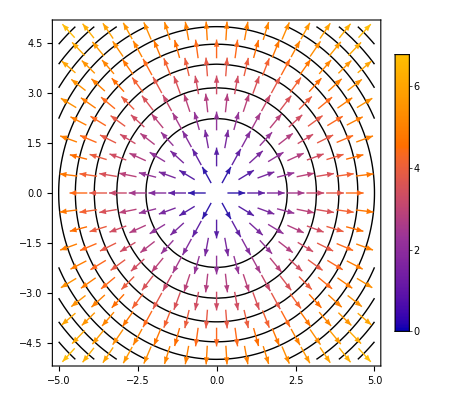

```mathematica
Show[ContourPlot[f,{x,-5,5},{y,-5,5}, ContourShading->None], VectorPlot[v, {x,-5,5}, {y,-5,5}, PlotLegends->Automatic]]
```

We then plot our vector value accordingly and it returns the graph above showing the direction of the gradient and the intensity radiating from the center outwards.

```mathematica
d = Div[v,{x,y}]
```

2

The divergence of the field is expected to be 2 as taking the partial derivative of the x part of the vector field with respect to x yields 1 and is  added to the partial derivative of the y part of the vector field with respect to y totaling 2.

```mathematica
c = Curl[Flatten[{v,0}],{x,y,z}]
```

{0,0,0}

Calculating the curl gives the expected value of 0i - 0j + 0k which matches our value.

Part 2: we are giving a new scalar field f(x,y,z) = -1/sqrt(x^2 + y^2 + z^2). We then calculate the gradient again and turn the new vector field from 3d to 2d by replacing the z component with 0.

```mathematica
f2 = -1 / Sqrt[x^2 + y^2 + z^2]
```

-1/(√(x^2+y^2+z^2))

```mathematica
v2 = Grad[f2,{x,y,z}]
```

{x/((x^2+y^2+z^2)^(3/2)),y/((x^2+y^2+z^2)^(3/2)),z/((x^2+y^2+z^2)^(3/2))}

```mathematica
f2d = f2 /. z-> 0
```

-1/(√(x^2+y^2))

```mathematica
v2d = v2 /. z->0
```

{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2)),0}

```mathematica
v2d1 = {v2d[[1]],v2d[[2]]}
```

{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))}

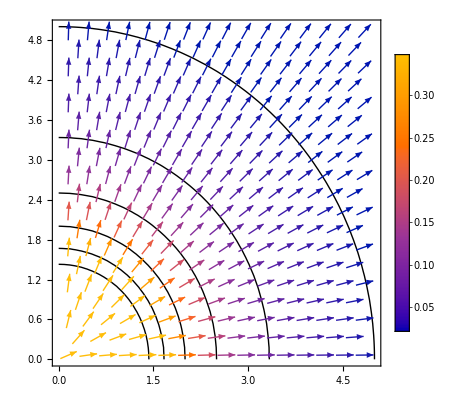

```mathematica
Show[ContourPlot[f2d,{x,0,5},{y,0,5}, ContourShading->None], VectorPlot[v2d1, {x,0,5}, {y,0,5},PlotLegends-> Automatic]]
```

Plotting this new vector field in the first quadrant only yields the graph above. Similar to the first graph but the intensity is now opposite direction.

```mathematica
d2 = Simplify[Div[v2,{x,y,z}]]
```

0

Calculating the divergence using the 3d version of the vector gives 0 which is unexpected.

```mathematica
tpc = ToPolarCoordinates[v2d]
```

{√(x^2/((x^2+y^2)^3)+y^2/((x^2+y^2)^3)),ArcCos[x/((x^2+y^2)^(3/2) √(x^2/((x^2+y^2)^3)+y^2/((x^2+y^2)^3)))],ArcTan[y/((x^2+y^2)^(3/2)),0]}

```mathematica
tpc2 = Simplify[tpc /. {x ->r Cos[θ], y -> r Sin[θ]}, Assumptions->r>0]
```

{1/r^2,ArcCos[Cos[θ]],ArcTan[Sin[θ],0]}

Using the ToPolarCoordinates function, to turn the vector without the z component in polar coordinates, we find that the values do not yield zero. The fields describe their motion.

Part 3: we are given the vector field v(x,y) + (iy + jx)/(x^2 + y^2). We then graph the field and find the curl.

```mathematica
v3 ={-y,x,0}/(x^2+y^2)
```

{-y/(x^2+y^2),x/(x^2+y^2),0}

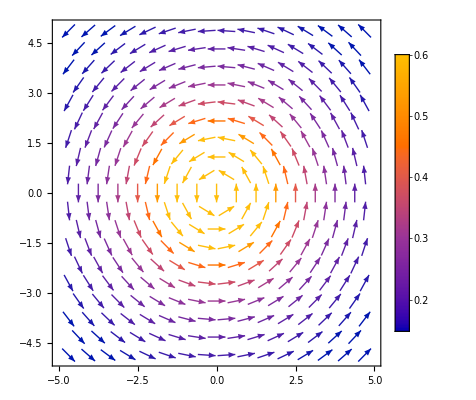

```mathematica
Show[VectorPlot[v3, {x,-5,5}, {y,-5,5},PlotLegends-> Automatic]]
```

The plot shows the movement in the shape of a circle.

```mathematica
v3
```

{-y/(x^2+y^2),x/(x^2+y^2)}

```mathematica
c3 = Simplify[Curl[Flatten[v3,0],{x,y,z}]]
```

{0,0,0}

The curl gives the surprising value of 0,0,0

```mathematica
tpc3 = ToPolarCoordinates[v3]
```

{√(x^2/((x^2+y^2)^2)+y^2/((x^2+y^2)^2)),ArcCos[-y/((x^2+y^2) √(x^2/((x^2+y^2)^2)+y^2/((x^2+y^2)^2)))],ArcTan[x/(x^2+y^2),0]}

```mathematica
tpc4 = Simplify[tpc3 /. {x ->r Cos[θ], y -> r Sin[θ]}, Assumptions->r>0]
```

{1/r,ArcCos[-Sin[θ]],ArcTan[Cos[θ],0]}